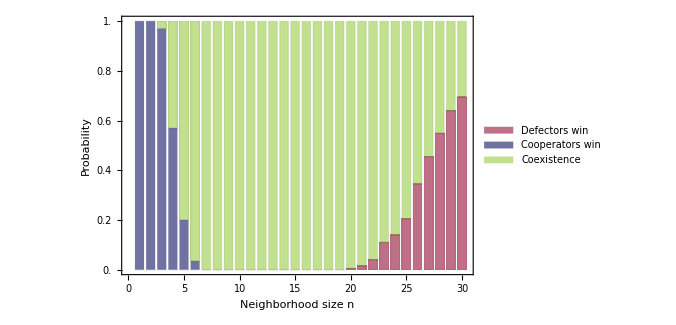

```mathematica
runs = Import[NotebookDirectory[]<>"StochasticBifurcationDiagram_groupsize.txt","Data"];
BarChart[runs/200,
ChartLayout->"Stacked",
FrameLabel->{{"Probability",None},{"Neighborhood size n",None}},
FrameTicks->{{Table[{j,j,{0,0}},{j,0.0,1.0,0.2}],None},{Table[{k,k,{0,0}},{k,0,30,5}],None}},
Frame->True,
FrameStyle->Directive[Thickness[0.0025],Black],
FrameTicksStyle->Opacity[1],FrameStyle->Opacity[1],
ChartStyle->{
Opacity[0.9,ColorData["DarkBands"][0.42]],
Opacity[1.0,ColorData["DarkBands"][0.78]],
Opacity[0.5,ColorData["AvocadoColors"][0.65]]
}(*"Rainbow"*),
ChartLegends->Placed[{"Defectors win","Cooperators win","Coexistence"},Above],
LabelStyle->{FontSize->22,Black,FontFamily->"Arial"},
FrameTicks->{{All,None},{All,None}},
AspectRatio->0.65
,ImageSize->500
]
```

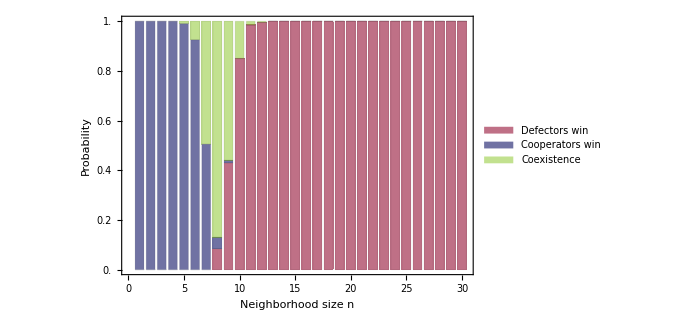

```mathematica
runs2 = Import[NotebookDirectory[]<>"StochasticBifurcationDiagram_groupsize_nocoexistence_30.txt","Data"];
Show[
BarChart[runs2/200,
ChartLayout->"Stacked",
FrameLabel->{{"Probability",None},{"Neighborhood size n",None}},
FrameTicks->{{Table[{j,j,{0,0}},{j,0.0,1.0,0.2}],None},{Table[{k,k,{0,0}},{k,0,30,5}],None}},
Frame->True,
FrameStyle->Directive[Thickness[0.0025],Black],
FrameTicksStyle->Opacity[1],FrameStyle->Opacity[1],
ChartStyle->{
Opacity[0.9,ColorData["DarkBands"][0.42]],
Opacity[1.0,ColorData["DarkBands"][0.78]],
Opacity[0.5,ColorData["AvocadoColors"][0.65]]
}(*"Rainbow"*),
ChartLegends->Placed[{"Defectors win","Cooperators win","Coexistence"},Above],
LabelStyle->{FontSize->22,Black,FontFamily->"Arial"},
FrameTicks->{{All,None},{All,None}},
AspectRatio->0.65
,ImageSize->500
]
]
```